```mathematica
Nc=1000;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-6;g=1;
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

```mathematica
ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)
```

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=1000;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
Nb=29;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

```mathematica
Block[{mQ=1},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
ΦB[x_]=ϕxB;
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
ΦB[x_]=ϕxB;
}
];
Print["Wavefunction build complete."];
(*Print[ϕn[#][Φ][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];]
```

Wavefunction build complete.

```mathematica
Table[Block[{ω1=0.907479105147823,ω2,x=0.5},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x])],{λ,Table[10^-m,{m,0,10}]}]
```

NIntegrate::ncvb: 在接近 {y} = {0.49999999985513617918936896507139741792684827729337238011453337094} 处的 y 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 3.49941×10^11 和 1.95287×10^6.

$Aborted

```mathematica
Block[{x=0.4,λ=10^-6},M1^2 ϕ1[x]-((m1^2-1)/x+(m2^2-1)/(1-x))ϕ1[x]+NIntegrate[ϕ1[y]/(x-y)^2,{y,0,x-λ}]+NIntegrate[ϕ1[y]/(x-y)^2,{y,x+λ,1}]-2/λ ϕ1[x]]
```

0.000224878

```mathematica
Block[{x=0.5,λ=10^-7},M1^2 ϕ1[x]-((m1^2-1)/x+(m2^2-1)/(1-x))ϕ1[x]+NIntegrate[ϕ1[y]/(x-y)^2,{y,0,x-λ},WorkingPrecision->50,PrecisionGoal->15,MaxRecursion->50]+NIntegrate[ϕ1[y]/(x-y)^2,{y,x+λ,1},WorkingPrecision->50,PrecisionGoal->15,MaxRecursion->50]-2/λ ϕ1[x]]
```

NIntegrate::precw: 参数函数的精度 ((1.12893 (-0.384205 √(1-Plus[«2»]^2)+1.89049×10^-12 Sin[2 ArcCos[-1+Times[«2»]]]+«72»+«950»))/(0.5-y)^2) 小于 WorkingPrecision (50.).

-0.0221158

```mathematica
Table[Block[{x=0.5,λ=10^-m},M1^2 ϕ1[x]-((m1^2-1)/x+(m2^2-1)/(1-x))ϕ1[x]+NIntegrate[ϕ1[y]/(x-y)^2,{y,0,x-λ}]+NIntegrate[ϕ1[y]/(x-y)^2,{y,x+λ,1}]-2/λ ϕ1[x]],{m,5,7,0.1}]
```

{-0.0514567,-0.0408736,-0.0324605,-0.0257953,-0.0204997,-0.0162689,-0.0129042,-0.0103119,-0.00813537,-0.00641519,-0.00515801,-0.00375516,-0.00301717,-0.00362319,-0.0014071,-0.0028903,-0.00424597,0.00189029,-0.00679996,-0.00614118,-0.0209826}

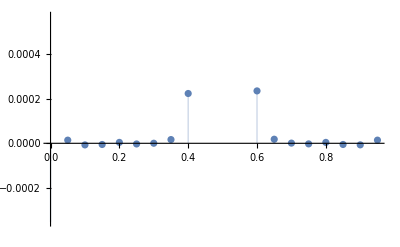

```mathematica
ListPlot[Table[{x,M1^2 ϕ1[x]-((m1^2-1)/x+(m2^2-1)/(1-x))ϕ1[x]+NIntegrate[ϕ1[y]/(x-y)^2,{y,0,x-λ}]+NIntegrate[ϕ1[y]/(x-y)^2,{y,x+λ,1}]-2/λ ϕ1[x]},{x,λ,1-λ,0.05}],Filling->Axis]
```

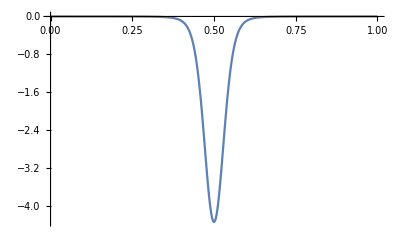

```mathematica
Plot[ϕ1[x],{x,0,1},PlotRange->All]
```

```mathematica
Plot[ω2p[ω1][M1,M2,M3,M4],{ω1,0,1}]
```